```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\WLEDUI.xlsx"]
```

```mathematica
data1={{10.,2.99},{11.,3.01},{12.,3.03},{12.9,3.05},{14.5,3.08},{16.,3.1},{17.5,3.12},{19.,3.14},{20.9,3.16},{22.9,3.18},{25.,3.21},{27.,3.24},{29.,3.26},{31.,3.28},{33.,3.3},{34.,3.32},{35.,3.33},{37.,3.35},{39.,3.38},{40.,3.39}}
```

{{10.,2.99},{11.,3.01},{12.,3.03},{12.9,3.05},{14.5,3.08},{16.,3.1},{17.5,3.12},{19.,3.14},{20.9,3.16},{22.9,3.18},{25.,3.21},{27.,3.24},{29.,3.26},{31.,3.28},{33.,3.3},{34.,3.32},{35.,3.33},{37.,3.35},{39.,3.38},{40.,3.39}}

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\BLEDUI.xlsx"]
```

```mathematica
data2={{10.,2.97},{11.,2.98},{12.,3.},{13.,3.01},{14.,3.02},{15.,3.03},{16.5,3.05},{18.,3.06},{20.,3.08},{22.,3.1},{24.,3.12},{25.4,3.14},{27.,3.13},{28.4,3.15},{30.,3.17},{31.5,3.18},{32.9,3.18},{34.,3.19}}
```

{{10.,2.97},{11.,2.98},{12.,3.},{13.,3.01},{14.,3.02},{15.,3.03},{16.5,3.05},{18.,3.06},{20.,3.08},{22.,3.1},{24.,3.12},{25.4,3.14},{27.,3.13},{28.4,3.15},{30.,3.17},{31.5,3.18},{32.9,3.18},{34.,3.19}}

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\GLEDUI.xlsx"]
```

```mathematica
data3={{10.,3.13},{11.4,3.15},{12.9,3.17},{15.,3.2},{16.5,3.21},{17.9,3.22},{19.5,3.24},{21.,3.25},{22.5,3.26},{24.,3.26},{25.4,3.28},{27.,3.29},{28.4,3.3},{30.,3.3},{32.,3.32},{34.,3.34},{35.9,3.36},{37.9,3.37},{40.,3.4}}
```

{{10.,3.13},{11.4,3.15},{12.9,3.17},{15.,3.2},{16.5,3.21},{17.9,3.22},{19.5,3.24},{21.,3.25},{22.5,3.26},{24.,3.26},{25.4,3.28},{27.,3.29},{28.4,3.3},{30.,3.3},{32.,3.32},{34.,3.34},{35.9,3.36},{37.9,3.37},{40.,3.4}}

```mathematica
a=LinearModelFit[data1,x,x]
```

FittedModel[2.88503+0.0127788 x]

```mathematica
b=LinearModelFit[data2,x,x]
```

FittedModel[2.89129+0.00914146 x]

```mathematica
c=LinearModelFit[data3,x,x]
```

FittedModel[3.06837+0.00813141 x]

```mathematica
a1=ListPlot[data1];
```

```mathematica
b1=ListPlot[data2];
```

```mathematica
c1=ListPlot[data3];
```

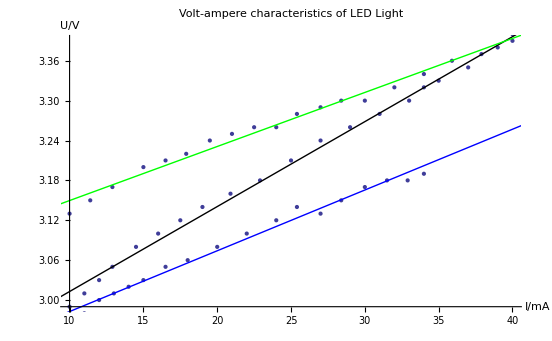

```mathematica
Show[a1,b1,c1,Plot[a[x],{x,0,50},PlotStyle->Black],Plot[b[x],{x,0,50},PlotStyle->Blue],Plot[c[x],{x,0,50},PlotStyle->Green],AxesLabel->{"I/mA","U/V"},PlotLabel->"Volt-ampere characteristics of LED Light"]
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\WUI.xlsx"]
```

```mathematica
data={{200.,1.43},{209.9,1.59},{220.,1.75},{229.9,1.92},{240.,2.1},{250.,2.3},{245.,2.21}}
```

{{200.,1.43},{209.9,1.59},{220.,1.75},{229.9,1.92},{240.,2.1},{250.,2.3},{245.,2.21}}

```mathematica
d=LinearModelFit[data,x,x]
```

FittedModel[-2.06512+0.017404 x]

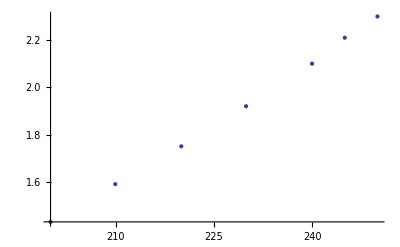

```mathematica
d1=ListPlot[data]
```

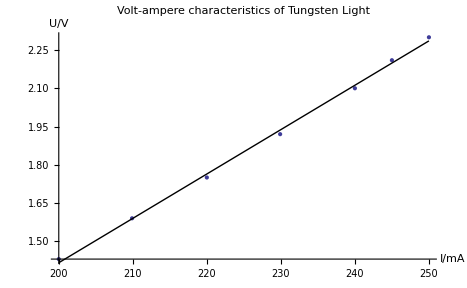

```mathematica
Show[d1,Plot[d[x],{x,200,250},PlotStyle->Black],AxesLabel->{"I/mA","U/V"},PlotLabel->"Volt-ampere characteristics of Tungsten Light"]
```